# Stable ODE

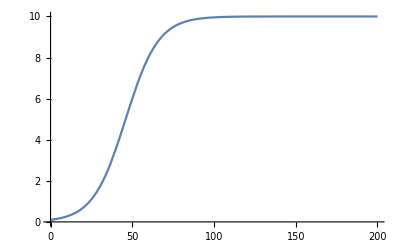

```mathematica
Block[{r=0.1,N0=10},Block[{s=NDSolve[{x'[t]==r x[t](1.0-x[t]/N0),x[0]==0.1},x[t],{t,0,200}]},Plot[Abs[x[t]/.s],{t,0,200}]]]
```

```mathematica
DSolve[{x'[t]==r x[t](1.0-x[t]/N0)},x[t],t]
```

{{x[t]→(2.71828^(r t+N0 C[1]) N0)/(-1.+2.71828^(r t+N0 C[1]))}}